# MOLD Projection Operators

## Preliminaries

We present an algorithm to construct Hermitean Young projection operators according to MOLD. To make life easier down the line, we define a function that gives all Young tableaux’  with n boxes in form of a list. (Already defined in InvariantAlgebras.nb and thus commented out)

```mathematica
(*Clear[YTableaux]
YTableaux[a_] := IntegerPartitions[a]//Tableaux/@#&//Flatten[#,1]&*)
```

## Determining the MOLD of a Young tableau

### Row- and Column-Words

The following function give the row-word and column-word respectively of a Young tableaux. (These are already defined in TransitionElements.nb)

```mathematica
Clear[RowWord,ColumnWord] 
RowWord[tableau_]:=tableau//Flatten
ColumnWord[tableau_]:=tableau//TransposeTableau//Flatten
```

### Order of a Tableau

We say that a Young tableau Θ is row-ordered, if its “row-word” is in lexical order. Similarly, we say that Θ is “column-ordered”, if its column-word is in lexical order. Lastly, we call Θ simply “ordered”, if either its row-word or its column word are in lexical order. The following functions RowOrderedQ, ColumnOrderedQ and TableauxOrderedQ test whether a tableau is row-ordered, column-ordered, or ordered respectively.

```mathematica
Clear[RowOrderedQ,ColumnOrderedQ,TableauOrderedQ];

RowOrderedQ[tableau_]:=Module[{},
If[(tableau//RowWord)==Table[i,{i,Length[tableau//Flatten]}],True,False]]

ColumnOrderedQ[tableau_]:=Module[{},
If[(tableau//ColumnWord)==Table[i,{i,Length[tableau//Flatten]}],True,False]]

TableauOrderedQ[tableau_]:=Module[{},
If[(tableau//RowWord)==Table[i,{i,Length[tableau//Flatten]}]||(tableau//ColumnWord)==Table[i,{i,Length[tableau//Flatten]}],True,False]]
```

For example, for all Young tableaux in Y_4, we check whether they have any specific ordering.

```mathematica
YTableaux[4];
%//TableauGrid/@#&
%%//RowOrderedQ/@#&
%%%//ColumnOrderedQ/@#&
%%%%//TableauOrderedQ/@#&
```

{1 | 2 | 3 | 4,1 | 3 | 4
2 |  | ,1 | 2 | 4
3 |  | ,1 | 2 | 3
4 |  | ,1 | 3
2 | 4,1 | 2
3 | 4,1 | 4
2 | 
3 | ,1 | 3
2 | 
4 | ,1 | 2
3 | 
4 | ,1
2
3
4}

{True,False,False,True,False,True,False,False,True,True}

{If[Global`TransposeTableau[{{1,2,3,4}}]=={1,2,3,4},True,False],If[Global`TransposeTableau[{{1,3,4},{2}}]=={1,2,3,4},True,False],If[Global`TransposeTableau[{{1,2,4},{3}}]=={1,2,3,4},True,False],If[Global`TransposeTableau[{{1,2,3},{4}}]=={1,2,3,4},True,False],If[Global`TransposeTableau[{{1,3},{2,4}}]=={1,2,3,4},True,False],If[Global`TransposeTableau[{{1,2},{3,4}}]=={1,2,3,4},True,False],If[Global`TransposeTableau[{{1,4},{2},{3}}]=={1,2,3,4},True,False],If[Global`TransposeTableau[{{1,3},{2},{4}}]=={1,2,3,4},True,False],If[Global`TransposeTableau[{{1,2},{3},{4}}]=={1,2,3,4},True,False],If[Global`TransposeTableau[{{1},{2},{3},{4}}]=={1,2,3,4},True,False]}

{True,If[Global`TransposeTableau[{{1,3,4},{2}}]=={1,2,3,4},True,False],If[Global`TransposeTableau[{{1,2,4},{3}}]=={1,2,3,4},True,False],True,If[Global`TransposeTableau[{{1,3},{2,4}}]=={1,2,3,4},True,False],True,If[Global`TransposeTableau[{{1,4},{2},{3}}]=={1,2,3,4},True,False],If[Global`TransposeTableau[{{1,3},{2},{4}}]=={1,2,3,4},True,False],True,True}

```mathematica
YTableaux[If[TransposeTableau[4]=={1},True,False]]
```

Tableaux[If[TransposeTableau[4]=={1},True,False]]

```mathematica
YTableaux[If[Flatten[4]=={1}||TransposeTableau[4]=={1},True,False]]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[4].

Tableaux[If[Flatten[4]=={1}||TransposeTableau[4]=={1},True,False]]

### MOLD and MOLD-Ancestry of a Tableau

In order to construct the Hermitean Young projection operator using MOLD in a later section, we need the MOLD ancestry of a Young tableau Θ. This ancestry includes all ancestor tableaux of Θ up to the most recent ancestor that is lexically ordered. The function MOLDTableauxAncestry gives a list of all MOLD-ancestors of Θ, ordered from the youngest to the oldes ancestor.
Similarly, the MOLD of Θ then merely becomes the length of this list.

```mathematica
Clear[MOLDTableauAncestry,MOLD]

MOLDTableauAncestry[tableau_]:=
MOLDTableauAncestry[tableau]=Module[{moldlist,tabl},
moldlist={};
tabl=tableau;
While[!(TableauOrderedQ[tabl]),tabl=tabl//Delete[#,Position[#,Max[#]]]&//(#//.{}->Sequence[])&;AppendTo[moldlist,tabl]];
moldlist
]

MOLD[tableau_]:=
MOLD[tableau]=Module[{},
Length[MOLDTableauAncestry[tableau]]
]
```

As an example, we have calculated the MOLD-ancestry of a particular tableau in Y_6. Thereafter, we have calculated the MOLD of each Young tableau in Y_5.

```mathematica
MOLDTableauAncestry[{{1,3,4},{2,5},{6}}]
```

{{{1,3,4},{2,5}},{{1,3,4},{2}}}

```mathematica
YTableaux[5];
%//TableauGrid/@#&
%%//MOLD/@#&
```

{1 | 2 | 3 | 4 | 5,1 | 3 | 4 | 5
2 |  |  | ,1 | 2 | 4 | 5
3 |  |  | ,1 | 2 | 3 | 5
4 |  |  | ,1 | 2 | 3 | 4
5 |  |  | ,1 | 3 | 5
2 | 4 | ,1 | 2 | 5
3 | 4 | ,1 | 3 | 4
2 | 5 | ,1 | 2 | 4
3 | 5 | ,1 | 2 | 3
4 | 5 | ,1 | 4 | 5
2 |  | 
3 |  | ,1 | 3 | 5
2 |  | 
4 |  | ,1 | 2 | 5
3 |  | 
4 |  | ,1 | 3 | 4
2 |  | 
5 |  | ,1 | 2 | 4
3 |  | 
5 |  | ,1 | 2 | 3
4 |  | 
5 |  | ,1 | 4
2 | 5
3 | ,1 | 3
2 | 5
4 | ,1 | 2
3 | 5
4 | ,1 | 3
2 | 4
5 | ,1 | 2
3 | 4
5 | ,1 | 5
2 | 
3 | 
4 | ,1 | 4
2 | 
3 | 
5 | ,1 | 3
2 | 
4 | 
5 | ,1 | 2
3 | 
4 | 
5 | ,1
2
3
4
5}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## Constructing the Hermitean Young Projection Operators Using MOLD (Product of S and AS)

### Four different Cases to distinguish

We now wish to construct the MOLD operator P_Θ corresponding to a particular Young tableau Θ. Let the MOLD of Θ be given by m. In accordance with the MOLD construction algorithm, we need to distinguish four cases:

	1.) m is even and Θ_(m) is row-ordered
	2.) m is even and Θ_(m) is column-ordered
	3.) m is odd and Θ_(m) is row-ordered
	4.) m is odd and Θ_(m) is column-ordered

We present a construction function for each of these four cases. These function will then later be combined into the function MOLDProjector, called MOLDProjectorEvenRow, MOLDProjectorEvenColumn, MOLDProjectorOddRow and MOLDProjectorOddColumn respectively

```mathematica
Clear[MOLDProjectorEvenRow,MOLDProjectorEvenColumn,MOLDProjectorOddRow,MOLDProjectorOddColumn]


(*For even MOLD m and Subscript[Θ, (m)] being row-ordered*)
MOLDProjectorEvenRow[tableau_]:=
MOLDProjectorEvenRow[tableau]=Module[{moldancestry,moldancestrysym,moldancestryasym,mold,syms,symcenter,asyms,asymcenter,Cand,CandDag,CenterProj,Projector},

moldancestry=Reverse[MOLDTableauAncestry[tableau]];
moldancestrysym=Delete[moldancestry,Table[{j},{j,2,moldancestry//Length,2}]];
moldancestryasym=Delete[moldancestry,Table[{j},{j,1,moldancestry//Length,2}]];

syms=moldancestrysym//(#/.{a_?IntegerQ}:>Sequence[])&//Map[S,#,{2}]&//Apply[T,#,{1}]&//(#//.T[S[a__]]:>S[a])&;

asyms=moldancestryasym//TransposeTableau/@#&//(#/.{a_?IntegerQ}:>Sequence[])&//Map[AS,#,{2}]&//Apply[T,#,{1}]&//(#//.T[AS[a__]]:>AS[a])&;

Cand=Riffle[syms,asyms];
CandDag=Reverse[Cand];


symcenter=tableau//(#/.{a_?IntegerQ}:>Sequence[])&//Table[S[#[[i]]],{i,#//Length}]&//Apply[T,#]&//(#//.T[S[a__]]:>S[a])&;
asymcenter=tableau//TransposeTableau//(#/.{a_?IntegerQ}:>Sequence[])&//Table[AS[#[[i]]],{i,#//Length}]&//Apply[T,#]&//(#//.T[AS[a__]]:>AS[a])&;
CenterProj={symcenter,asymcenter,symcenter};

Projector=Join[Cand,CenterProj,CandDag]//YP@@#&;

Projector
]


(*For even MOLD m and Subscript[Θ, (m)] being column-ordered*)
MOLDProjectorEvenColumn[tableau_]:=
MOLDProjectorEvenColumn[tableau]=Module[{moldancestry,moldancestrysym,moldancestryasym,mold,syms,symcenter,asyms,asymcenter,Cand,CandDag,CenterProj,Projector},

moldancestry=Reverse[MOLDTableauAncestry[tableau]];
moldancestrysym=Delete[moldancestry,Table[{j},{j,1,moldancestry//Length,2}]];
moldancestryasym=Delete[moldancestry,Table[{j},{j,2,moldancestry//Length,2}]];

syms=moldancestrysym//(#/.{a_?IntegerQ}:>Sequence[])&//Map[S,#,{2}]&//Apply[T,#,{1}]&//(#//.T[S[a__]]:>S[a])&;

asyms=moldancestryasym//TransposeTableau/@#&//(#/.{a_?IntegerQ}:>Sequence[])&//Map[AS,#,{2}]&//Apply[T,#,{1}]&//(#//.T[AS[a__]]:>AS[a])&;

Cand=Riffle[asyms,syms];
CandDag=Reverse[Cand];


symcenter=tableau//(#/.{a_?IntegerQ}:>Sequence[])&//Table[S[#[[i]]],{i,#//Length}]&//Apply[T,#]&//(#//.T[S[a__]]:>S[a])&;
asymcenter=tableau//TransposeTableau//(#/.{a_?IntegerQ}:>Sequence[])&//Table[AS[#[[i]]],{i,#//Length}]&//Apply[T,#]&//(#//.T[AS[a__]]:>AS[a])&;
CenterProj={asymcenter,symcenter,asymcenter};

Projector=Join[Cand,CenterProj,CandDag]//YP@@#&;

Projector
]


(*For odd MOLD m and Subscript[Θ, (m)] being row-ordered*)
MOLDProjectorOddRow[tableau_]:=
MOLDProjectorOddRow[tableau]=Module[{moldancestry,moldancestrysym,moldancestryasym,mold,syms,symcenter,asyms,asymcenter,Cand,CandDag,CenterProj,Projector},

moldancestry=Reverse[MOLDTableauAncestry[tableau]];
moldancestrysym=Delete[moldancestry,Table[{j},{j,2,moldancestry//Length,2}]];
moldancestryasym=Delete[moldancestry,Table[{j},{j,1,moldancestry//Length,2}]];

syms=moldancestrysym//(#/.{a_?IntegerQ}:>Sequence[])&//Map[S,#,{2}]&//Apply[T,#,{1}]&//(#//.T[S[a__]]:>S[a])&;

asyms=moldancestryasym//TransposeTableau/@#&//(#/.{a_?IntegerQ}:>Sequence[])&//Map[AS,#,{2}]&//Apply[T,#,{1}]&//(#//.T[AS[a__]]:>AS[a])&;

Cand=Riffle[syms,asyms];
CandDag=Reverse[Cand];


symcenter=tableau//(#/.{a_?IntegerQ}:>Sequence[])&//Table[S[#[[i]]],{i,#//Length}]&//Apply[T,#]&//(#//.T[S[a__]]:>S[a])&;
asymcenter=tableau//TransposeTableau//(#/.{a_?IntegerQ}:>Sequence[])&//Table[AS[#[[i]]],{i,#//Length}]&//Apply[T,#]&//(#//.T[AS[a__]]:>AS[a])&;
CenterProj={asymcenter,symcenter,asymcenter};

Projector=Join[Cand,CenterProj,CandDag]//YP@@#&;

Projector
]


(*For odd MOLD m and Subscript[Θ, (m)] being column-ordered*)
MOLDProjectorOddColumn[tableau_]:=
MOLDProjectorOddColumn[tableau]=Module[{moldancestry,moldancestrysym,moldancestryasym,mold,syms,symcenter,asyms,asymcenter,Cand,CandDag,CenterProj,Projector},

moldancestry=Reverse[MOLDTableauAncestry[tableau]];
moldancestrysym=Delete[moldancestry,Table[{j},{j,1,moldancestry//Length,2}]];
moldancestryasym=Delete[moldancestry,Table[{j},{j,2,moldancestry//Length,2}]];

syms=moldancestrysym//(#/.{a_?IntegerQ}:>Sequence[])&//Map[S,#,{2}]&//Apply[T,#,{1}]&//(#//.T[S[a__]]:>S[a])&;

asyms=moldancestryasym//TransposeTableau/@#&//(#/.{a_?IntegerQ}:>Sequence[])&//Map[AS,#,{2}]&//Apply[T,#,{1}]&//(#//.T[AS[a__]]:>AS[a])&;

Cand=Riffle[asyms,syms];
CandDag=Reverse[Cand];


symcenter=tableau//(#/.{a_?IntegerQ}:>Sequence[])&//Table[S[#[[i]]],{i,#//Length}]&//Apply[T,#]&//(#//.T[S[a__]]:>S[a])&;
asymcenter=tableau//TransposeTableau//(#/.{a_?IntegerQ}:>Sequence[])&//Table[AS[#[[i]]],{i,#//Length}]&//Apply[T,#]&//(#//.T[AS[a__]]:>AS[a])&;
CenterProj={symcenter,asymcenter,symcenter};

Projector=Join[Cand,CenterProj,CandDag]//YP@@#&;

Projector
]
```

We now give four examples, one for each of the cases we distinguished. In these examples, we have manually determined whether the MOLD of the tableau Θ is even or odd, and whether Θ_(m) is row- or column-ordered. Thus, we manually chose the appropriate function to construct the MOLD operator. From these examples it is clear, that the MOLD operators need very littly cleaning up after being built. In fact, only the last operator needs minor cosmetics, the other three do not require any alterations.

```mathematica
{{1,2,3,7},{4,6,8},{5,9}}
%//TableauGrid
%%//MOLDProjectorEvenRow
%//graphicalYP
```

{{1,2,3,7},{4,6,8},{5,9}}

1 | 2 | 3 | 7
4 | 6 | 8 | 
5 | 9 |  |

T[S[{1,2,3,7}],S[{4,6,8}],S[{5,9}]]≀AS[{{1,2,3,7},{4,6,8},{5,9}}]≀T[S[{1,2,3,7}],S[{4,6,8}],S[{5,9}]]

-Graphics-

```mathematica
{{1,4,7,8},{2,5,9},{3},{6}};
%//TableauGrid
%%//MOLDProjectorEvenColumn
%//graphicalYP
```

1 | 4 | 7 | 8
2 | 5 | 9 | 
3 |  |  | 
6 |  |  |

AS[{{1,4,7,8},{2,5,9}}]≀T[S[{1,4,7,8}],S[{2,5,9}]]≀AS[{{1,4,7,8},{2,5,9}}]

-Graphics-

```mathematica
{{1,2,3,7},{4,5,8},{6,9}};
%//TableauGrid
%%//MOLDProjectorOddRow
%//graphicalYP
```

1 | 2 | 3 | 7
4 | 5 | 8 | 
6 | 9 |  |

AS[{{1,2,3,7},{4,5,8},{6,9}}]≀T[S[{1,2,3,7}],S[{4,5,8}],S[{6,9}]]≀AS[{{1,2,3,7},{4,5,8},{6,9}}]

-Graphics-

```mathematica
{{1,4,6,9},{2,7,8},{3},{5}};
%//TableauGrid
%%//MOLDProjectorOddColumn
%//graphicalYP
%%//FixedPoint[(#//simplifyFormHermiteanYoungProjector//simplifyT)&,#]&
%//graphicalYP
```

1 | 4 | 6 | 9
2 | 7 | 8 | 
3 |  |  | 
5 |  |  |

T[S[{1,4,6,9}],S[{2,7,8}]]≀AS[{{1,4,6,9},{2,7,8}}]≀T[S[{1,4,6,9}],S[{2,7,8}]]

-Graphics-

AS[{{1,4,6,9},{2,7,8}}]≀T[S[{1,4,6,9}],S[{2,7,8}]]

-Graphics-

```mathematica
{{1, 4, 6, 9}, {2, 7, 8, }, {3, , , }, {5, , , }}
```

1 | 4 | 6 | 9
2 | 7 | 8 | 
3 |  |  | 
5 |  |  |

### One Function for a General MOLD Projector

We will now define one function to construct the MOLD operator corresponding to a particular tableau. This function will automatically choose which one of the above four defined functions is appropriate for the particular tableau in question and then use this function to construct the MOLD operator

```mathematica
Clear[MOLDProjector,SymmetrizerQ,AntiSymmetrizerQ]

SymmetrizerQ[tableau_]:=Module[{},
If[tableau=={Table[i,{i,Length[tableau//Flatten]}]},True,False]]
AntiSymmetrizerQ[tableau_]:=Module[{},
If[tableau==({Table[i,{i,Length[tableau//Flatten]}]}//Transpose),True,False]]

MOLDProjector[tableau_]:=Module[{},
(*Print[symmetrizer];*)
tableau//S@@#&//YP@#&]/;SymmetrizerQ[tableau]

MOLDProjector[tableau_]:=Module[{},
(*Print[antisymmetrizer];*)
tableau//Transpose//AS@@#&//YP@#&]/;AntiSymmetrizerQ[tableau]

MOLDProjector[tableau_]:=
MOLDOperator[tableau]=Module[{moldancestor},
moldancestor=Join[{tableau},tableau//MOLDTableauAncestry]//Last;
If[EvenQ[MOLD[tableau]],
If[RowOrderedQ[moldancestor],
MOLDProjectorEvenRow[tableau]//(#//.T[]:>Sequence[])&,
MOLDProjectorEvenColumn[tableau]]//(#//.T[]:>Sequence[])&,
If[RowOrderedQ[moldancestor],
MOLDProjectorOddRow[tableau]//(#//.T[]:>Sequence[])&,
MOLDProjectorOddColumn[tableau]//(#//.T[]:>Sequence[])&]
]
]

(*Clear[SimplifyMOLDOperator]
SimplifyMOLDOperator[tableau_]:=tableau//(#//.)*)
```

We will now calculate all MOLD operators of the nq-algebra, for various values of n.

{1 | 2 | 3,1 | 3
2 | ,1 | 2
3 | ,1
2
3}

{YP[S[{1,2,3}]],AS[{{1,3}}]≀S[{1,3}]≀AS[{{1,3}}],S[{1,2}]≀AS[{{1,2}}]≀S[{1,2}],YP[AS[{1,2,3}]]}

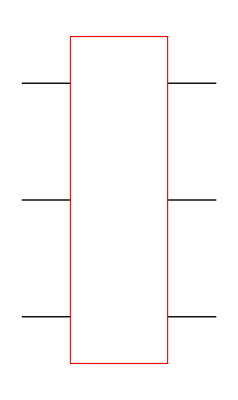
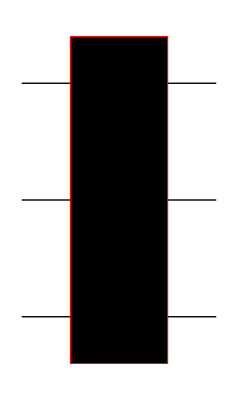
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
YTableaux[3];
%//TableauGrid/@#&
%%//MOLDProjector/@#&
(*%//FixedPoint[(#//simplifyFormHermiteanYoungProjector//simplifyT)&,#]&*)
%//graphicalYP/@#&
```

{1 | 2 | 3 | 4 | 5,1 | 3 | 4 | 5
2 |  |  | ,1 | 2 | 4 | 5
3 |  |  | ,1 | 2 | 3 | 5
4 |  |  | ,1 | 2 | 3 | 4
5 |  |  | ,1 | 3 | 5
2 | 4 | ,1 | 2 | 5
3 | 4 | ,1 | 3 | 4
2 | 5 | ,1 | 2 | 4
3 | 5 | ,1 | 2 | 3
4 | 5 | ,1 | 4 | 5
2 |  | 
3 |  | ,1 | 3 | 5
2 |  | 
4 |  | ,1 | 2 | 5
3 |  | 
4 |  | ,1 | 3 | 4
2 |  | 
5 |  | ,1 | 2 | 4
3 |  | 
5 |  | ,1 | 2 | 3
4 |  | 
5 |  | ,1 | 4
2 | 5
3 | ,1 | 3
2 | 5
4 | ,1 | 2
3 | 5
4 | ,1 | 3
2 | 4
5 | ,1 | 2
3 | 4
5 | ,1 | 5
2 | 
3 | 
4 | ,1 | 4
2 | 
3 | 
5 | ,1 | 3
2 | 
4 | 
5 | ,1 | 2
3 | 
4 | 
5 | ,1
2
3
4
5}

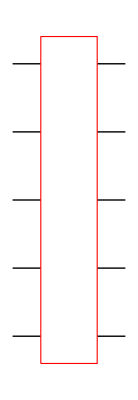
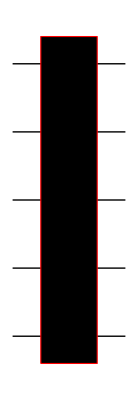
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
YTableaux[5];
%//TableauGrid/@#&
%%//MOLDProjector/@#&;
%//graphicalYP/@#&
%%//FixedPoint[(#//simplifyFormHermiteanYoungProjector//simplifyT)&,#]&;
%//graphicalYP/@#&
```

{1 | 2 | 3 | 4 | 5 | 6 | 7,1 | 3 | 4 | 5 | 6 | 7
2 |  |  |  |  | ,1 | 2 | 4 | 5 | 6 | 7
3 |  |  |  |  | ,1 | 2 | 3 | 5 | 6 | 7
4 |  |  |  |  | ,1 | 2 | 3 | 4 | 6 | 7
5 |  |  |  |  | ,1 | 2 | 3 | 4 | 5 | 7
6 |  |  |  |  | ,1 | 2 | 3 | 4 | 5 | 6
7 |  |  |  |  | ,1 | 3 | 5 | 6 | 7
2 | 4 |  |  | ,1 | 2 | 5 | 6 | 7
3 | 4 |  |  | ,1 | 3 | 4 | 6 | 7
2 | 5 |  |  | ,1 | 2 | 4 | 6 | 7
3 | 5 |  |  | ,1 | 2 | 3 | 6 | 7
4 | 5 |  |  | ,1 | 3 | 4 | 5 | 7
2 | 6 |  |  | ,1 | 2 | 4 | 5 | 7
3 | 6 |  |  | ,1 | 2 | 3 | 5 | 7
4 | 6 |  |  | ,1 | 2 | 3 | 4 | 7
5 | 6 |  |  | ,1 | 3 | 4 | 5 | 6
2 | 7 |  |  | ,1 | 2 | 4 | 5 | 6
3 | 7 |  |  | ,1 | 2 | 3 | 5 | 6
4 | 7 |  |  | ,1 | 2 | 3 | 4 | 6
5 | 7 |  |  | ,1 | 2 | 3 | 4 | 5
6 | 7 |  |  | ,1 | 4 | 5 | 6 | 7
2 |  |  |  | 
3 |  |  |  | ,1 | 3 | 5 | 6 | 7
2 |  |  |  | 
4 |  |  |  | ,1 | 2 | 5 | 6 | 7
3 |  |  |  | 
4 |  |  |  | ,1 | 3 | 4 | 6 | 7
2 |  |  |  | 
5 |  |  |  | ,1 | 2 | 4 | 6 | 7
3 |  |  |  | 
5 |  |  |  | ,1 | 2 | 3 | 6 | 7
4 |  |  |  | 
5 |  |  |  | ,1 | 3 | 4 | 5 | 7
2 |  |  |  | 
6 |  |  |  | ,1 | 2 | 4 | 5 | 7
3 |  |  |  | 
6 |  |  |  | ,1 | 2 | 3 | 5 | 7
4 |  |  |  | 
6 |  |  |  | ,1 | 2 | 3 | 4 | 7
5 |  |  |  | 
6 |  |  |  | ,1 | 3 | 4 | 5 | 6
2 |  |  |  | 
7 |  |  |  | ,1 | 2 | 4 | 5 | 6
3 |  |  |  | 
7 |  |  |  | ,1 | 2 | 3 | 5 | 6
4 |  |  |  | 
7 |  |  |  | ,1 | 2 | 3 | 4 | 6
5 |  |  |  | 
7 |  |  |  | ,1 | 2 | 3 | 4 | 5
6 |  |  |  | 
7 |  |  |  | ,1 | 3 | 5 | 7
2 | 4 | 6 | ,1 | 2 | 5 | 7
3 | 4 | 6 | ,1 | 3 | 4 | 7
2 | 5 | 6 | ,1 | 2 | 4 | 7
3 | 5 | 6 | ,1 | 2 | 3 | 7
4 | 5 | 6 | ,1 | 3 | 5 | 6
2 | 4 | 7 | ,1 | 2 | 5 | 6
3 | 4 | 7 | ,1 | 3 | 4 | 6
2 | 5 | 7 | ,1 | 2 | 4 | 6
3 | 5 | 7 | ,1 | 2 | 3 | 6
4 | 5 | 7 | ,1 | 3 | 4 | 5
2 | 6 | 7 | ,1 | 2 | 4 | 5
3 | 6 | 7 | ,1 | 2 | 3 | 5
4 | 6 | 7 | ,1 | 2 | 3 | 4
5 | 6 | 7 | ,1 | 4 | 6 | 7
2 | 5 |  | 
3 |  |  | ,1 | 3 | 6 | 7
2 | 5 |  | 
4 |  |  | ,1 | 2 | 6 | 7
3 | 5 |  | 
4 |  |  | ,1 | 3 | 6 | 7
2 | 4 |  | 
5 |  |  | ,1 | 2 | 6 | 7
3 | 4 |  | 
5 |  |  | ,1 | 4 | 5 | 7
2 | 6 |  | 
3 |  |  | ,1 | 3 | 5 | 7
2 | 6 |  | 
4 |  |  | ,1 | 2 | 5 | 7
3 | 6 |  | 
4 |  |  | ,1 | 3 | 4 | 7
2 | 6 |  | 
5 |  |  | ,1 | 2 | 4 | 7
3 | 6 |  | 
5 |  |  | ,1 | 2 | 3 | 7
4 | 6 |  | 
5 |  |  | ,1 | 3 | 5 | 7
2 | 4 |  | 
6 |  |  | ,1 | 2 | 5 | 7
3 | 4 |  | 
6 |  |  | ,1 | 3 | 4 | 7
2 | 5 |  | 
6 |  |  | ,1 | 2 | 4 | 7
3 | 5 |  | 
6 |  |  | ,1 | 2 | 3 | 7
4 | 5 |  | 
6 |  |  | ,1 | 4 | 5 | 6
2 | 7 |  | 
3 |  |  | ,1 | 3 | 5 | 6
2 | 7 |  | 
4 |  |  | ,1 | 2 | 5 | 6
3 | 7 |  | 
4 |  |  | ,1 | 3 | 4 | 6
2 | 7 |  | 
5 |  |  | ,1 | 2 | 4 | 6
3 | 7 |  | 
5 |  |  | ,1 | 2 | 3 | 6
4 | 7 |  | 
5 |  |  | ,1 | 3 | 4 | 5
2 | 7 |  | 
6 |  |  | ,1 | 2 | 4 | 5
3 | 7 |  | 
6 |  |  | ,1 | 2 | 3 | 5
4 | 7 |  | 
6 |  |  | ,1 | 2 | 3 | 4
5 | 7 |  | 
6 |  |  | ,1 | 3 | 5 | 6
2 | 4 |  | 
7 |  |  | ,1 | 2 | 5 | 6
3 | 4 |  | 
7 |  |  | ,1 | 3 | 4 | 6
2 | 5 |  | 
7 |  |  | ,1 | 2 | 4 | 6
3 | 5 |  | 
7 |  |  | ,1 | 2 | 3 | 6
4 | 5 |  | 
7 |  |  | ,1 | 3 | 4 | 5
2 | 6 |  | 
7 |  |  | ,1 | 2 | 4 | 5
3 | 6 |  | 
7 |  |  | ,1 | 2 | 3 | 5
4 | 6 |  | 
7 |  |  | ,1 | 2 | 3 | 4
5 | 6 |  | 
7 |  |  | ,1 | 5 | 6 | 7
2 |  |  | 
3 |  |  | 
4 |  |  | ,1 | 4 | 6 | 7
2 |  |  | 
3 |  |  | 
5 |  |  | ,1 | 3 | 6 | 7
2 |  |  | 
4 |  |  | 
5 |  |  | ,1 | 2 | 6 | 7
3 |  |  | 
4 |  |  | 
5 |  |  | ,1 | 4 | 5 | 7
2 |  |  | 
3 |  |  | 
6 |  |  | ,1 | 3 | 5 | 7
2 |  |  | 
4 |  |  | 
6 |  |  | ,1 | 2 | 5 | 7
3 |  |  | 
4 |  |  | 
6 |  |  | ,1 | 3 | 4 | 7
2 |  |  | 
5 |  |  | 
6 |  |  | ,1 | 2 | 4 | 7
3 |  |  | 
5 |  |  | 
6 |  |  | ,1 | 2 | 3 | 7
4 |  |  | 
5 |  |  | 
6 |  |  | ,1 | 4 | 5 | 6
2 |  |  | 
3 |  |  | 
7 |  |  | ,1 | 3 | 5 | 6
2 |  |  | 
4 |  |  | 
7 |  |  | ,1 | 2 | 5 | 6
3 |  |  | 
4 |  |  | 
7 |  |  | ,1 | 3 | 4 | 6
2 |  |  | 
5 |  |  | 
7 |  |  | ,1 | 2 | 4 | 6
3 |  |  | 
5 |  |  | 
7 |  |  | ,1 | 2 | 3 | 6
4 |  |  | 
5 |  |  | 
7 |  |  | ,1 | 3 | 4 | 5
2 |  |  | 
6 |  |  | 
7 |  |  | ,1 | 2 | 4 | 5
3 |  |  | 
6 |  |  | 
7 |  |  | ,1 | 2 | 3 | 5
4 |  |  | 
6 |  |  | 
7 |  |  | ,1 | 2 | 3 | 4
5 |  |  | 
6 |  |  | 
7 |  |  | ,1 | 4 | 6
2 | 5 | 7
3 |  | ,1 | 3 | 6
2 | 5 | 7
4 |  | ,1 | 2 | 6
3 | 5 | 7
4 |  | ,1 | 3 | 6
2 | 4 | 7
5 |  | ,1 | 2 | 6
3 | 4 | 7
5 |  | ,1 | 4 | 5
2 | 6 | 7
3 |  | ,1 | 3 | 5
2 | 6 | 7
4 |  | ,1 | 2 | 5
3 | 6 | 7
4 |  | ,1 | 3 | 4
2 | 6 | 7
5 |  | ,1 | 2 | 4
3 | 6 | 7
5 |  | ,1 | 2 | 3
4 | 6 | 7
5 |  | ,1 | 3 | 5
2 | 4 | 7
6 |  | ,1 | 2 | 5
3 | 4 | 7
6 |  | ,1 | 3 | 4
2 | 5 | 7
6 |  | ,1 | 2 | 4
3 | 5 | 7
6 |  | ,1 | 2 | 3
4 | 5 | 7
6 |  | ,1 | 3 | 5
2 | 4 | 6
7 |  | ,1 | 2 | 5
3 | 4 | 6
7 |  | ,1 | 3 | 4
2 | 5 | 6
7 |  | ,1 | 2 | 4
3 | 5 | 6
7 |  | ,1 | 2 | 3
4 | 5 | 6
7 |  | ,1 | 4 | 7
2 | 5 | 
3 | 6 | ,1 | 3 | 7
2 | 5 | 
4 | 6 | ,1 | 2 | 7
3 | 5 | 
4 | 6 | ,1 | 3 | 7
2 | 4 | 
5 | 6 | ,1 | 2 | 7
3 | 4 | 
5 | 6 | ,1 | 4 | 6
2 | 5 | 
3 | 7 | ,1 | 3 | 6
2 | 5 | 
4 | 7 | ,1 | 2 | 6
3 | 5 | 
4 | 7 | ,1 | 3 | 6
2 | 4 | 
5 | 7 | ,1 | 2 | 6
3 | 4 | 
5 | 7 | ,1 | 4 | 5
2 | 6 | 
3 | 7 | ,1 | 3 | 5
2 | 6 | 
4 | 7 | ,1 | 2 | 5
3 | 6 | 
4 | 7 | ,1 | 3 | 4
2 | 6 | 
5 | 7 | ,1 | 2 | 4
3 | 6 | 
5 | 7 | ,1 | 2 | 3
4 | 6 | 
5 | 7 | ,1 | 3 | 5
2 | 4 | 
6 | 7 | ,1 | 2 | 5
3 | 4 | 
6 | 7 | ,1 | 3 | 4
2 | 5 | 
6 | 7 | ,1 | 2 | 4
3 | 5 | 
6 | 7 | ,1 | 2 | 3
4 | 5 | 
6 | 7 | ,1 | 5 | 7
2 | 6 | 
3 |  | 
4 |  | ,1 | 4 | 7
2 | 6 | 
3 |  | 
5 |  | ,1 | 3 | 7
2 | 6 | 
4 |  | 
5 |  | ,1 | 2 | 7
3 | 6 | 
4 |  | 
5 |  | ,1 | 4 | 7
2 | 5 | 
3 |  | 
6 |  | ,1 | 3 | 7
2 | 5 | 
4 |  | 
6 |  | ,1 | 2 | 7
3 | 5 | 
4 |  | 
6 |  | ,1 | 3 | 7
2 | 4 | 
5 |  | 
6 |  | ,1 | 2 | 7
3 | 4 | 
5 |  | 
6 |  | ,1 | 5 | 6
2 | 7 | 
3 |  | 
4 |  | ,1 | 4 | 6
2 | 7 | 
3 |  | 
5 |  | ,1 | 3 | 6
2 | 7 | 
4 |  | 
5 |  | ,1 | 2 | 6
3 | 7 | 
4 |  | 
5 |  | ,1 | 4 | 5
2 | 7 | 
3 |  | 
6 |  | ,1 | 3 | 5
2 | 7 | 
4 |  | 
6 |  | ,1 | 2 | 5
3 | 7 | 
4 |  | 
6 |  | ,1 | 3 | 4
2 | 7 | 
5 |  | 
6 |  | ,1 | 2 | 4
3 | 7 | 
5 |  | 
6 |  | ,1 | 2 | 3
4 | 7 | 
5 |  | 
6 |  | ,1 | 4 | 6
2 | 5 | 
3 |  | 
7 |  | ,1 | 3 | 6
2 | 5 | 
4 |  | 
7 |  | ,1 | 2 | 6
3 | 5 | 
4 |  | 
7 |  | ,1 | 3 | 6
2 | 4 | 
5 |  | 
7 |  | ,1 | 2 | 6
3 | 4 | 
5 |  | 
7 |  | ,1 | 4 | 5
2 | 6 | 
3 |  | 
7 |  | ,1 | 3 | 5
2 | 6 | 
4 |  | 
7 |  | ,1 | 2 | 5
3 | 6 | 
4 |  | 
7 |  | ,1 | 3 | 4
2 | 6 | 
5 |  | 
7 |  | ,1 | 2 | 4
3 | 6 | 
5 |  | 
7 |  | ,1 | 2 | 3
4 | 6 | 
5 |  | 
7 |  | ,1 | 3 | 5
2 | 4 | 
6 |  | 
7 |  | ,1 | 2 | 5
3 | 4 | 
6 |  | 
7 |  | ,1 | 3 | 4
2 | 5 | 
6 |  | 
7 |  | ,1 | 2 | 4
3 | 5 | 
6 |  | 
7 |  | ,1 | 2 | 3
4 | 5 | 
6 |  | 
7 |  | ,1 | 6 | 7
2 |  | 
3 |  | 
4 |  | 
5 |  | ,1 | 5 | 7
2 |  | 
3 |  | 
4 |  | 
6 |  | ,1 | 4 | 7
2 |  | 
3 |  | 
5 |  | 
6 |  | ,1 | 3 | 7
2 |  | 
4 |  | 
5 |  | 
6 |  | ,1 | 2 | 7
3 |  | 
4 |  | 
5 |  | 
6 |  | ,1 | 5 | 6
2 |  | 
3 |  | 
4 |  | 
7 |  | ,1 | 4 | 6
2 |  | 
3 |  | 
5 |  | 
7 |  | ,1 | 3 | 6
2 |  | 
4 |  | 
5 |  | 
7 |  | ,1 | 2 | 6
3 |  | 
4 |  | 
5 |  | 
7 |  | ,1 | 4 | 5
2 |  | 
3 |  | 
6 |  | 
7 |  | ,1 | 3 | 5
2 |  | 
4 |  | 
6 |  | 
7 |  | ,1 | 2 | 5
3 |  | 
4 |  | 
6 |  | 
7 |  | ,1 | 3 | 4
2 |  | 
5 |  | 
6 |  | 
7 |  | ,1 | 2 | 4
3 |  | 
5 |  | 
6 |  | 
7 |  | ,1 | 2 | 3
4 |  | 
5 |  | 
6 |  | 
7 |  | ,1 | 5
2 | 6
3 | 7
4 | ,1 | 4
2 | 6
3 | 7
5 | ,1 | 3
2 | 6
4 | 7
5 | ,1 | 2
3 | 6
4 | 7
5 | ,1 | 4
2 | 5
3 | 7
6 | ,1 | 3
2 | 5
4 | 7
6 | ,1 | 2
3 | 5
4 | 7
6 | ,1 | 3
2 | 4
5 | 7
6 | ,1 | 2
3 | 4
5 | 7
6 | ,1 | 4
2 | 5
3 | 6
7 | ,1 | 3
2 | 5
4 | 6
7 | ,1 | 2
3 | 5
4 | 6
7 | ,1 | 3
2 | 4
5 | 6
7 | ,1 | 2
3 | 4
5 | 6
7 | ,1 | 6
2 | 7
3 | 
4 | 
5 | ,1 | 5
2 | 7
3 | 
4 | 
6 | ,1 | 4
2 | 7
3 | 
5 | 
6 | ,1 | 3
2 | 7
4 | 
5 | 
6 | ,1 | 2
3 | 7
4 | 
5 | 
6 | ,1 | 5
2 | 6
3 | 
4 | 
7 | ,1 | 4
2 | 6
3 | 
5 | 
7 | ,1 | 3
2 | 6
4 | 
5 | 
7 | ,1 | 2
3 | 6
4 | 
5 | 
7 | ,1 | 4
2 | 5
3 | 
6 | 
7 | ,1 | 3
2 | 5
4 | 
6 | 
7 | ,1 | 2
3 | 5
4 | 
6 | 
7 | ,1 | 3
2 | 4
5 | 
6 | 
7 | ,1 | 2
3 | 4
5 | 
6 | 
7 | ,1 | 7
2 | 
3 | 
4 | 
5 | 
6 | ,1 | 6
2 | 
3 | 
4 | 
5 | 
7 | ,1 | 5
2 | 
3 | 
4 | 
6 | 
7 | ,1 | 4
2 | 
3 | 
5 | 
6 | 
7 | ,1 | 3
2 | 
4 | 
5 | 
6 | 
7 | ,1 | 2
3 | 
4 | 
5 | 
6 | 
7 | ,1
2
3
4
5
6
7}

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

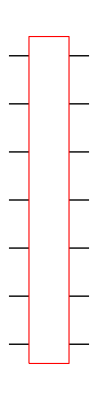
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
YTableaux[7];
%//TableauGrid/@#&
%%//MOLDProjector/@#&;
%//(#//.T[]:>Sequence[])&;
%//FixedPoint[(#//simplifyFormHermiteanYoungProjector//simplifyT)&,#]&;
%//graphicalYP/@#&
```

To generate all MOLD operators for the 8q-algebra. The last command saves the birdtrack as a pdf. Since this takes a fair amount of time, it is commented out here.

```mathematica
(*YTableaux[8];
%//TableauGrid/@#&
%%//MOLDProjector/@#&;
%//(#//.T[]:>Sequence[])&;
%//FixedPoint[(#//simplifyFormHermiteanYoungProjector//simplifyT)&,#]&;
%//graphicalYP/@#&
%//Table[Export["P8-"<>ToString[i]<>".pdf",#[[i]]],{i,#//Length}]&*)
```

## MOLD Hermitean Young Projection Operators (As a Coefficient Vector)

```mathematica
(*Needs InvariantAlgebra.nb*)
```

We have constructed the MOLD operators as products of S and AS, which allowed us to present them graphically using “graphicalYP”. However, to perform calculations using Mathematica’s built-in functions from the Combinatorica package, we need to be able to write the operators as coefficient vectors. We accomplish this using the function “yPToVec” defined in InvariantAlgebra.nb. In order to calculate the coefficient vector, one needs to specify tableau in the argument of “MOLDProjectorVec”.
It should be noted that these coefficient vectors are already properly normalized due to the function “normalizationFactorVec” in the following definition.

```mathematica
Clear[MOLDProjectorVec]

MOLDProjectorVec[tableau_]:=
MOLDProjectorVec[tableau]=Module[{moldprojectorvec},
moldprojectorvec=tableau//MOLDProjector//(# /. a_YP :> yPToVec[PermAlg[tableau//Flatten//Length]][a]) & // (normalizationFactorVec[PermAlg[tableau//Flatten//Length]][#] #) &;

moldprojectorvec
]

MOLDProjectorVec[tableau_,dimension_]:=
MOLDProjectorVec[tableau,dimension]=Module[{moldprojectorvec},
moldprojectorvec=tableau//MOLDProjector//(# /. a_YP :> yPToVec[PermAlg[dimension]][a]) & // (normalizationFactorVec[PermAlg[dimension]][#] #) &;

moldprojectorvec
]
```

As an example, we calculated all MOLD projection operators as coefficient vectors for the 4q-algebra. We have then verified that they are indeed orthogonal to each other

```mathematica
YTableaux[4];
%//TableauGrid/@#&
%%//MOLDProjectorVec/@#&
%//Table[Vprod[PermAlg[4]][#[[i]],#[[i]]]-#[[i]],{i,1,10}]&//MatrixPlot
```

{1 | 2 | 3 | 4,1 | 3 | 4
2 |  | ,1 | 2 | 4
3 |  | ,1 | 2 | 3
4 |  | ,1 | 3
2 | 4,1 | 2
3 | 4,1 | 4
2 | 
3 | ,1 | 3
2 | 
4 | ,1 | 2
3 | 
4 | ,1
2
3
4}

{{1/(576 Vprod[PermAlg[4]][{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24},{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24}]),1/(576 Vprod[PermAlg[4]][{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24},{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24}]),1/(576 Vprod[PermAlg[4]][{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24},{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24}]),1/(576 Vprod[PermAlg[4]][{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24},{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24}]),1/(576 Vprod[PermAlg[4]][{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24},{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24}]),1/(576 Vprod[PermAlg[4]][{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24},{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24}]),1/(576 Vprod[PermAlg[4]][{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24},{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24}]),1/(576 Vprod[PermAlg[4]][{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24},{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24}]),1/(576 Vprod[PermAlg[4]][{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24},{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24}]),1/(576 Vprod[PermAlg[4]][{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24},{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24}]),1/(576 Vprod[PermAlg[4]][{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24},{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24}]),1/(576 Vprod[PermAlg[4]][{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24},{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24}]),1/(576 Vprod[PermAlg[4]][{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24},{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24}]),1/(576 Vprod[PermAlg[4]][{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24},{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24}]),1/(576 Vprod[PermAlg[4]][{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24},{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24}]),1/(576 Vprod[PermAlg[4]][{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24},{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24}]),1/(576 Vprod[PermAlg[4]][{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24},{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24}]),1/(576 Vprod[PermAlg[4]][{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24},{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24}]),1/(576 Vprod[PermAlg[4]][{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24},{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24}]),1/(576 Vprod[PermAlg[4]][{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24},{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24}]),1/(576 Vprod[PermAlg[4]][{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24},{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24}]),1/(576 Vprod[PermAlg[4]][{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24},{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24}]),1/(576 Vprod[PermAlg[4]][{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24},{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24}]),1/(576 Vprod[PermAlg[4]][{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24},{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24}])},0,0,0,0,0,0,0,0,{1/(576 Vprod[PermAlg[4]][{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24},{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24}]),-(1/(576 Vprod[PermAlg[4]][{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24},{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24}])),-(1/(576 Vprod[PermAlg[4]][{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24},{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24}])),1/(576 Vprod[PermAlg[4]][{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24},{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24}]),1/(576 Vprod[PermAlg[4]][{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24},{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24}]),-(1/(576 Vprod[PermAlg[4]][{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24},{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24}])),-(1/(576 Vprod[PermAlg[4]][{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24},{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24}])),1/(576 Vprod[PermAlg[4]][{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24},{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24}]),1/(576 Vprod[PermAlg[4]][{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24},{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24}]),-(1/(576 Vprod[PermAlg[4]][{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24},{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24}])),-(1/(576 Vprod[PermAlg[4]][{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24},{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24}])),1/(576 Vprod[PermAlg[4]][{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24},{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24}]),1/(576 Vprod[PermAlg[4]][{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24},{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24}]),-(1/(576 Vprod[PermAlg[4]][{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24},{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24}])),-(1/(576 Vprod[PermAlg[4]][{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24},{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24}])),1/(576 Vprod[PermAlg[4]][{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24},{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24}]),1/(576 Vprod[PermAlg[4]][{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24},{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24}]),-(1/(576 Vprod[PermAlg[4]][{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24},{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24}])),-(1/(576 Vprod[PermAlg[4]][{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24},{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24}])),1/(576 Vprod[PermAlg[4]][{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24},{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24}]),1/(576 Vprod[PermAlg[4]][{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24},{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24}]),-(1/(576 Vprod[PermAlg[4]][{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24},{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24}])),-(1/(576 Vprod[PermAlg[4]][{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24},{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24}])),1/(576 Vprod[PermAlg[4]][{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24},{1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24,1/24,-1/24,-1/24,1/24}])}}

MatrixPlot::mat0: Argument {«1»} at position 1 is not a matrix.

MatrixPlot[{1}]
 |  |  |  |

## Early Trials

Carrying the algorithm out manually

```mathematica
(*Clear[tableau];

tableau[1]={{1,3,4},{2,5}};
tableau[1]//RowWord
Table[i,{i,Length[tableau[1]//Flatten]}]
!((tableau[1]//RowWord)==Table[i,{i,Length[tableau[1]//Flatten]}])

tableau[2]=tableau[1]//Delete[#,Position[#,Max[#]]]&//(#//.{}->Sequence[])&
tableau[2]//RowWord
Table[i,{i,Length[tableau[2]//Flatten]}]
!((tableau[2]//RowWord)==Table[i,{i,Length[tableau[2]//Flatten]}])

tableau[3]=tableau[2]//Delete[#,Position[#,Max[#]]]&//(#//.{}->Sequence[])&
tableau[3]//RowWord
Table[i,{i,Length[tableau[3]//Flatten]}]
!((tableau[3]//RowWord)==Table[i,{i,Length[tableau[3]//Flatten]}])

tableau[4]=tableau[3]//Delete[#,Position[#,Max[#]]]&//(#//.{}->Sequence[])&
tableau[4]//RowWord
Table[i,{i,Length[tableau[4]//Flatten]}]
!((tableau[4]//RowWord)==Table[i,{i,Length[tableau[4]//Flatten]}])*)
```

These functions return the tableau if it is ordered, and the parent tableau if it is not ordered

```mathematica
(*Clear[FirstTestFunctionRow,FirstTestFunctionColumn]

FirstTestFunctionRow[tabl_]:=If[(tabl//RowWord)==Table[i,{i,Length[tabl//Flatten]}],tabl,tabl//Delete[#,Position[#,Max[#]]]&//(#//.{}->Sequence[])&]

FirstTestFunctionColumn[tabl_]:=If[(tabl//ColumnWord)==Table[i,{i,Length[tabl//Flatten]}],tabl,tabl//Delete[#,Position[#,Max[#]]]&//(#//.{}->Sequence[])&]

Clear[FirstTestFunctionRowColumn]

FirstTestFunctionRowColumn[tabl_]:=If[(tabl//RowWord)==Table[i,{i,Length[tabl//Flatten]}]||(tabl//ColumnWord)==Table[i,{i,Length[tabl//Flatten]}],tabl,tabl//Delete[#,Position[#,Max[#]]]&//(#//.{}->Sequence[])&]*)
```

Examples to the above defined functions

```mathematica
(*YTableaux[4]//FirstTestFunctionRow/@#&;
%//TableauGrid/@#&
FirstTestFunctionColumn[YTableaux[4][[2]]]*)
```

```mathematica
(*YTableaux[4]//FirstTestFunctionRowColumn/@#&;
%//TableauGrid/@#&*)
```